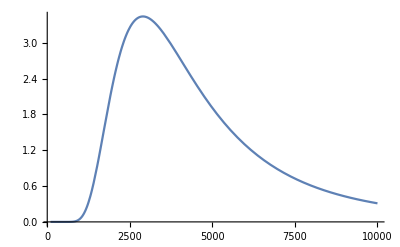

```mathematica
(* https://www.expii.com/solve/47/4 *)

(* The color of a candle flame is mostly determined by its temperature, which is on the order of 1,000 degrees Kelvin. Planck’s law of black-body radiation states that for an object at a given absolute temperature T in Kelvin,the distribution of spectral radiance over wavelength is:
\frac{2h c^2}{\lambda^5}\frac{1}{e^{\frac{hc}{\lambda kT}}-1}
where h is Planck’s constant,c is the speed of light, \lambda is the wavelength of the emitted light,and k is Boltzmanns constant. At 1000 degrees Kelvin, what is the peak wavelength of the light emitted,
rounded to the nearest nanometer? *)

hc=2*Pi*197.32/10^6; (*MeV nm*)
k = 8.617*10^-11; (* MeV/K*)
f[l_,t_]:=10^20/(l^5(Exp[hc/(l k t)]-1));
Plot[f[l,1000],{l,100,10000}]
```

```mathematica
FindMaximum[f[l,1000],{l,3000}]
```

{3.43867,{l→2897.78}}